# Math II-Calculus II Project 2

# I. Approximation and Non Elementary Integral

Use Trapezoidal rule and Simpson’s rule to approximate the values of the integrals below for n = 10, 20, 30, 40, 50 and 100. Please construct a table containing the result similar to Table 8.5 in the lecture slides of Chapter 8. Each group must choose the exercise according to the group number.

VI. ∫_0^0.5 1/(√(1-x^2))ⅆx

### Trapezoidal rule: Tn= Δx/2[ f(x_0) + 2f(x_1) + 2f(x_2) + 2f(x_3) +.....+ 2f(x_(n-1)) + f(x_n) ] For better readability, we can group f(x_0) and f(x_n) and any function that is multiply by 2. Tn= Δx/2[ f(x_0) + f(x_n) +2[f(x_1) + f(x_2) + f(x_3) +.....+ f(x_(n-1))] ] Δx is the base length of each trapezoid and n is the subinterval between the lower and upper bound Δx =(b-a)/n x_0=a x_n=b 2[f(x_1) + f(x_2) + f(x_3) +.....+ f(x_(n-1))] =2∑_(i=1)^(n-1) f[a+(i*Δx)] We can rewrite it as: Tn= Δx/2[ f(a) + f(b) +2∑_(i=1)^(n-1) f[a+(i*Δx] ]

### Simpson’s rule: Sn= Δx/3[ f(x_0) + 4f(x_1) + 2f(x_2) + 4f(x_3) +.....+ 2f(x_(n-2))+ 4f(x_(n-1)) + f(x_n) ] For better readability, we can group f(x_0) and f(x_n) and any function that is multiply by 2 and 4. Sn= Δx/3[ f(x_0) + f(x_n) +4[f(x_1) + f(x_3) + f(x_5) +.....+ f(x_(n-1))] +2[f(x_2) + f(x_4) + f(x_6) +.....+ f(x_(n-2))]] 4[f(x_1) + f(x_3) + f(x_5) +.....+ f(x_(n-1))]= 4Sum[ f[a+i( Δx) ] ,{ i, 1, n-1, 2} ] 2[f(x_2) + f(x_4) + f(x_6) +.....+ f(x_(n-2))]= 2Sum[ f[a+i( Δx) ] ,{ i,2,n-1,2} ] We can rewrite it as: Sn= Δx/2[ f(x_0) + f(x_n) + 4Sum[ f[a+i(Δx ) ] ,{ i, 1, n-1, 2} ]+2Sum[ f[a+i( Δx) ] ,{ i,2,n-1,2 } ]]

### Trapezoidal rule:

```mathematica
f[x_]=1/(√(1-x^2));
```

```mathematica
a=0;
b=0.5;
```

```mathematica
DeltaX[n_]:=(b-a)/n;
```

```mathematica
Tn[n_] =DeltaX[n]/2 (( f[a]+ f[b] )+(2∑_(i=1)^(n-1) f[a+i*DeltaX[n]]));
```

```mathematica
Tn[10]
```

0.523759

Simpson’s rule:

```mathematica
Sn[n_]:=(DeltaX[n]/3)*(f[a]+f[b]+4*Sum[f[a+i*(DeltaX[n])],{i,1,n-1,2}]+2*Sum[f[a+i*(DeltaX[n])],{i,2,n-1,2}]);
```

```mathematica
Sn[10]
```

0.523599

### Calculate the Margin of Error (Trapezoid and Simpson)

### E_(T≤)(K(b-a))^3/(12 n^2)

K is the maximum value of the second derivative f”(x) within the bound [a,b]

```mathematica
f2[x_]=D[f[x],{x,2}]
```

(3 x^2)/((1-x^2)^(5/2))+1/((1-x^2)^(3/2))

```mathematica
K=MaxValue[f2[x],{0<=x<=0.5},x]
```

3.0792

```mathematica
f2[0]
```

1

```mathematica
f2[0.5]
```

3.0792

```mathematica
ET[n_]=(K(0.5-0)^3)/(12*(n)^2);
```

```mathematica
ET[10]
```

0.00032075

### E_s≤(K(b-a))^5/(180 n^4)

K is the maximum value of the fourth derivative f””(x) within the bound [a,b]

```mathematica
f4[x_]=D[f[x],{x,4}]
```

(105 x^4)/((1-x^2)^(9/2))+(90 x^2)/((1-x^2)^(7/2))+9/((1-x^2)^(5/2))

```mathematica
M=MaxValue[f4[x],{0<=x<=0.5},x];
```

```mathematica
f4[0]
```

9

```mathematica
f4[0.5]
```

104.009

```mathematica
ES[n_]=(M(0.5-0)^5)/(180*(n)^4);
```

```mathematica
ES[10]
```

1.8057×10^-6

```mathematica
Integral=N[Integrate[f[x],{x,0,0.5}]]
```

0.523599

### Table

```mathematica
TableForm[Table[{n,N[Tn[n],20], N[ET[n],20]  , N[Sn[n], 20], N[ES[n],20]},{n,{10,20,30,40,50,100}}],TableHeadings->{{Integral},{"n","Trapezoid", "Et", "Simpson", "Es"}}]//N //Magnify[#,1.1]&
```

| n | Trapezoid | Et | Simpson | Es
0.523599 | 10. | 0.523759 | 0.000104167 K | Sn[10.] | 1.8057×10^-6
 | 20. | 0.523639 | 0.0000260417 K | Sn[20.] | 1.12857×10^-7
 | 30. | 0.523617 | 0.0000115741 K | Sn[30.] | 2.22926×10^-8
 | 40. | 0.523609 | 6.51042×10^-6 K | Sn[40.] | 7.05353×10^-9
 | 50. | 0.523605 | 4.16667×10^-6 K | Sn[50.] | 2.88913×10^-9
 | 100. | 0.5236 | 1.04167×10^-6 K | Sn[100.] | 1.8057×10^-10

### Trapezoidal Rule Graphical

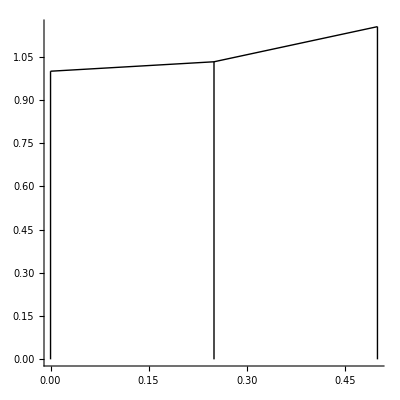

```mathematica
visualTrapezoidRule[func_,xmin_,xmax_,steps_,aspect_:Automatic]:=Module[{pts,verticals,caps},pts=Table[{x,func[x]},{x,Subdivide[xmin,xmax,steps]}];
verticals=Line[{{#[[1]],0},#}]&/@pts;
caps=Line@pts;
Graphics[{verticals,caps},AspectRatio->aspect,Axes->True]]
Trapezoidal=visualTrapezoidRule[f[x]&,0,1/2,2,1]
```

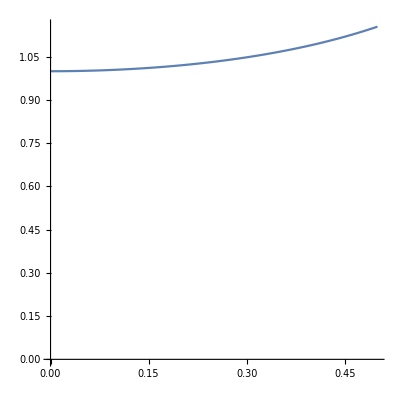

```mathematica
line=Plot[{1/(√(1-x^2))},{x,0,0.5},AspectRatio->1,Axes->True,AxesOrigin->{0,0}]
```

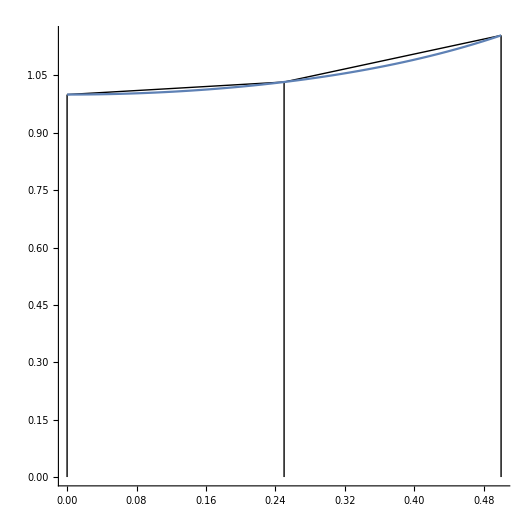

```mathematica
Show[Trapezoidal,line]
```

### Simpson’s rule visualization

```mathematica
visualSimpsonRule[func_,xmin_,xmax_,steps_,aspect_:Automatic]:=Module[{pts,verticals,caps},pts=Table[{x,func[x]},{x,Subdivide[xmin,xmax,steps]}];
verticals=Line[{{#[[1]],0},#}]&/@pts;
caps=BSplineCurve[pts];
Graphics[{verticals,caps},AspectRatio->aspect,Axes->True]]
Simpson=visualSimpsonRule[f[#]&,0,1/2,4,1]
```

-Graphics-

```mathematica
Show[Simpson,line]
```

-Graphics-

# II. Problem 1: Drug assimilation

## An average adult under the age of 60 assimilates a 12-h cold medicine into his or her system at a rate modeled by dy/dt=6-ln(2t^2-3t+3) where y is measured in milligrams and t is the time in hours since the medication was taken. What amount of medicine is absorbed into a person’s system over a 12-h period?

dy=6-ln(2t^2-3t+3)dt
∫1ⅆy=∫6-ln(2 t^2-3t+3)ⅆt
y=∫6-ln(2 t^2-3t+3)ⅆt
Let y(t)=6-ln(2 t^2-3t+3)

```mathematica
y[t_]=6-Log[3+(2*t^2)-(3*t)];
```

Simpson’s rule
Sn= Δy/3[ y(t_0) + y(t_n) +4[y(t_1) + y(t_3) + y(t_5) +.....+y(t_(n-1))] +2[y(t_2) + y(t_4) + y(t_6) +.....+ y(t_(n-2))]]

```mathematica
DeltaY[a_,b_,n_]:=(b-a)/n;
```

```mathematica
Sn[f_,a_,b_,n_]:=DeltaY[a,b,n]/3*(f[a]+f[b]+4*Sum[f[a+i*(DeltaY[a,b,n])],{i,1,n-1,2}]+2*Sum[f[a+i*(DeltaY[a,b,n])],{i,2,n-1,2}]);
```

```mathematica
N[Sn[y[#]&,0,12,10]];
```

```mathematica
Exact=NIntegrate[y[t],{t,0,12}];
```

# Graph of overall medicine consumed (mg)

```mathematica
NSolve[6-log(2 t^2-3 t+3)==0,t]
```

{{t→-13.4196},{t→14.9196}}

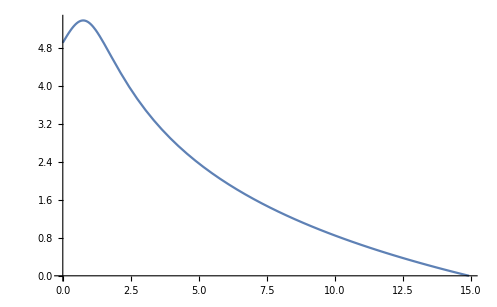

```mathematica
Plot[y[t],{t,0,14.91957645},Axes->True]
```

```mathematica
Overall=N[Sn[y[#]&,0,14.91957645,100]]
```

29.3292

```mathematica
Percent[f_,a_,b_,n_]:=(Sn[f,a,b,n]/Overall)*100;
```

```mathematica
Percent[y[#]&,0,12,100]
```

97.8034

### Table

```mathematica
TableForm[Table[{N[Sn[y[#]&,a,b,n],20]},{n,{10}},{a,{0}},{b,{1,2,3,4,5,6,7,8,9,10,11,12}}],TableHeadings->{None,{"Time  Medicine Absorbed(mg)"},{"1hr","2hr","3hr","4hr","5hr","6hr","7hr","8hr","9hr","10hr","11hr","12hr"}}]//N //Magnify[#,2]&
```

Time  Medicine Absorbed(mg)
1hr | 5.23718
2hr | 10.1224
3hr | 14.0539
4hr | 17.2283
5hr | 19.8326
6hr | 21.9898
7hr | 23.7818
8hr | 25.264
9hr | 26.4748
10hr | 27.4423
11hr | 28.1882
12hr | 28.7307

So after 12hr we can estimated that 28.73mg of medicine is being absorbed (n=10). However, we can increase the accuracy by increasing the value of n.

```mathematica
TableForm[Table[{N[Sn[y[#]&,a,b,n],20]},{n,{100}},{a,{0}},{b,{1,2,3,4,5,6,7,8,9,10,11,12}}],TableHeadings->{None,{"Time  Medicine Absorbed(mg)"},{"1hr","2hr","3hr","4hr","5hr","6hr","7hr","8hr","9hr","10hr","11hr","12hr"}}]//N //Magnify[#,2]&
```

Time  Medicine Absorbed(mg)
1hr | 5.23718
2hr | 10.1224
3hr | 14.0539
4hr | 17.2283
5hr | 19.832
6hr | 21.9851
7hr | 23.7679
8hr | 25.237
9hr | 26.4343
10hr | 27.392
11hr | 28.1353
12hr | 28.685

The table above uses n=100.

Percentage of medicine the body absorbed

```mathematica
TableForm[Table[{N[Percent[y[#]&,a,b,n],20]},{n,{100}},{a,{0}},{b,{1,2,3,4,5,6,7,8,9,10,11,12,13,14.919}}],TableHeadings->{None,{"Time  Percentage of medicine absorbed"},{"1hr","2hr","3hr","4hr","5hr","6hr","7hr","8hr","9hr","10hr","11hr","12hr","13hr","14hr"}}]//N //Magnify[#,2]&
```

Time  Percentage of medicine absorbed
1hr | 17.8565
2hr | 34.513
3hr | 47.9176
4hr | 58.7411
5hr | 67.6185
6hr | 74.9597
7hr | 81.0383
8hr | 86.0474
9hr | 90.1297
10hr | 93.3948
11hr | 95.9293
12hr | 97.8034
13hr | 99.0751
14hr | 100.